```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Function Definitions

```mathematica
kfinal={0.6802525363662164,-0.31465604392609736};(*100k run*)
kfinalu={0.9017845365143496,-0.3669424499609976};
kfinall={0.4587205362180833,-0.26236963789119705};
αcont={0.5146004500017507,0.002579680095957094};(*10k run*)
σcont={0.16904257426266697,0.0009046347484072015};
ccont={-0.15782092474161866,0.0024785523617348124};
conv=0.197327;
rsbvac=1.542442506842263/conv;
Tset={0.15,0.16,0.165,0.17,0.18,0.19,0.2,0.25,0.3};
TsetS={"T=150MeV","T=160MeV","T=165MeV","T=170MeV","T=180MeV","T=190MeV","T=200MeV","T=250MeV","T=300MeV","Vacuum"};
```

```mathematica
mDcalmu[T_,μ_,c_,d_]:=Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ];
```

```mathematica
ReVs[r_,mD_,σ_]:=(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
ReVc[r_,mD_,α_,c_]:=c-α mD-α Exp[-mD r]/r;
ReV[r_,mD_,α_,σ_,c_]:=c-α mD-α Exp[-mD r]/r+(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
ReVm0[r_,α_,σ_,c_]:=c-α/r+σ r;
```

```mathematica
ImVc1[r_,mD_,α_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4]);
ImVc[r_,mD_,α_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞},MaxRecursion->20]];
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
ImVssb[r_,mD_,σ_,T_,rsb_]:=If[r<rsb,1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4],1/4 mD √π rsb^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 rsb^2)/4]];
ImV[r_,mD_,α_,σ_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞}]]+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

## Plots for physical values

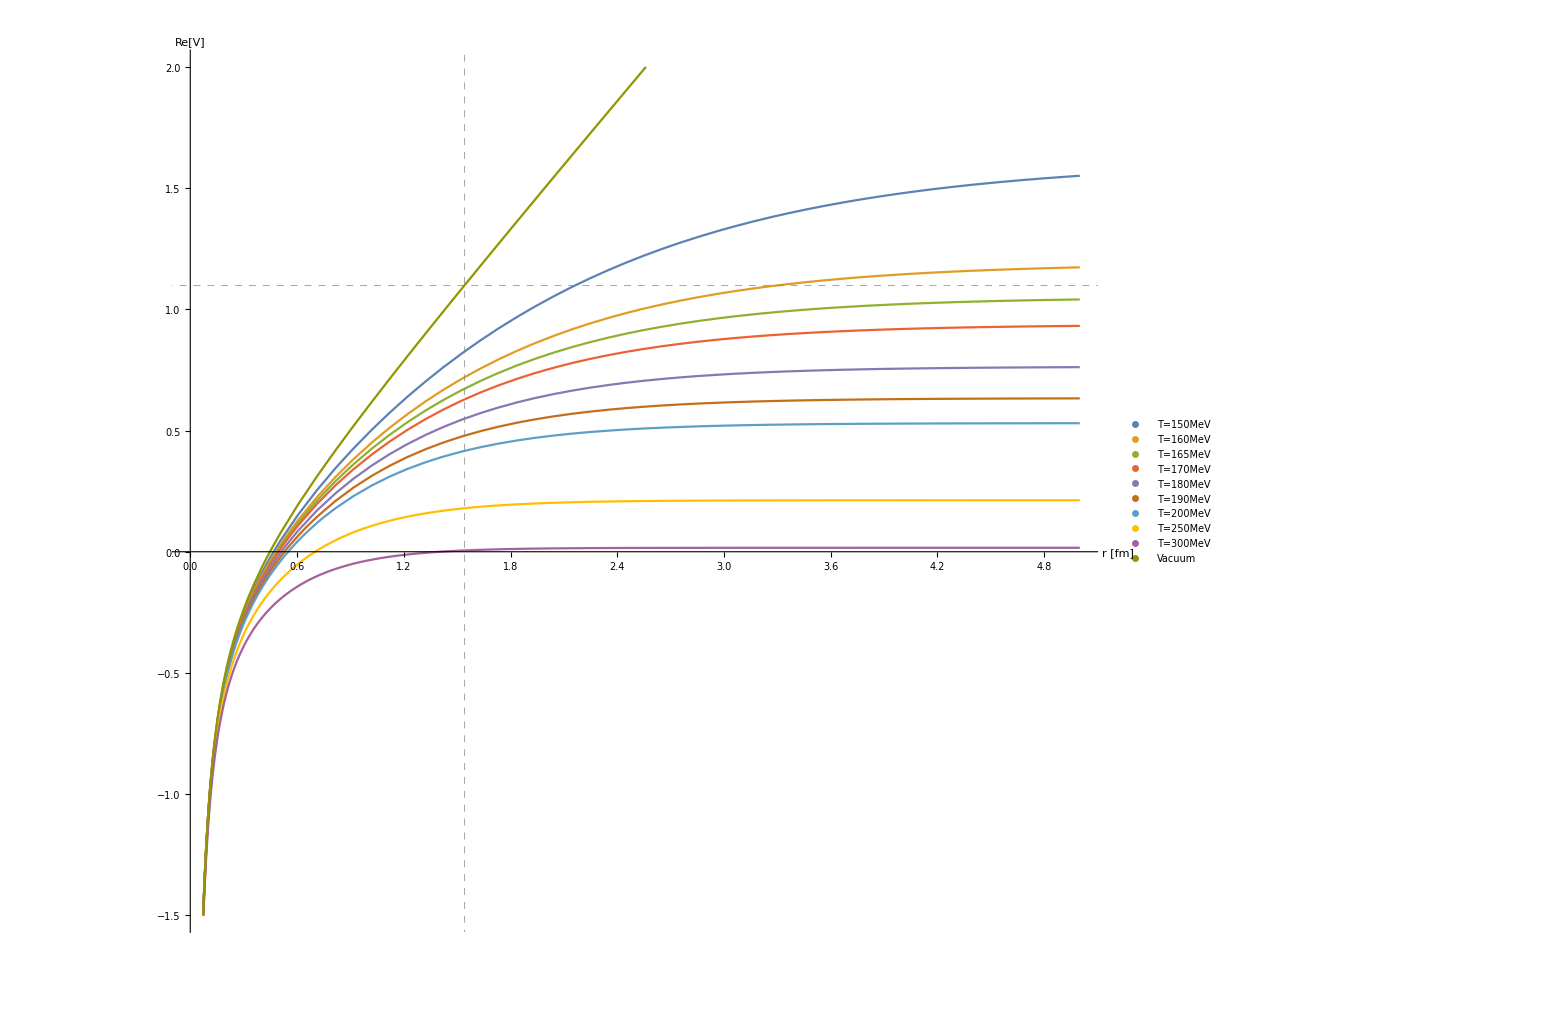

```mathematica
Plot[{ReV[r/0.197,mDcalmu[Tset[[1]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[2]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[3]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[4]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[5]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[6]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[7]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[8]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[9]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{rsbvac conv},{ReVm0[rsbvac,αcont[[1]],σcont[[1]],ccont[[1]]]}},GridLinesStyle->Directive[Gray, Dashed],PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.8,0.95}],BaseStyle->{FontSize->14}]
```

```mathematica
ReVas[t_]:=ccont[[1]]-αcont[[1]]mDcalmu[t,0,kfinal[[1]],kfinal[[2]]]+(2 σcont[[1]])/mDcalmu[t,0,kfinal[[1]],kfinal[[2]]];
```

```mathematica
rsbth=Table[{t,r/.FindRoot[ReV[r/0.197,mDcalmu[t/1000,0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==0.999ReVas[t/1000],{r,1/10,1/100,10}]},{t,170,300,10}]
```

{{170,6.39467},{180,5.64985},{190,5.11657},{200,4.7139},{210,4.40776},{220,4.16253},{230,3.96097},{240,3.79529},{250,3.66085},{260,3.55578},{270,3.48153},{280,3.44565},{290,3.47282},{300,3.6874}}

```mathematica
mdinv=Table[{t,conv/mDcalmu[t/1000,0,kfinal[[1]],kfinal[[2]]]},{t,150,300,10}]
```

{{150,1.08798},{160,0.855893},{170,0.721273},{180,0.63156},{190,0.566487},{200,0.516531},{210,0.477741},{220,0.445811},{230,0.418587},{240,0.395021},{250,0.374366},{260,0.356073},{270,0.339729},{280,0.325014},{290,0.311679},{300,0.299525}}

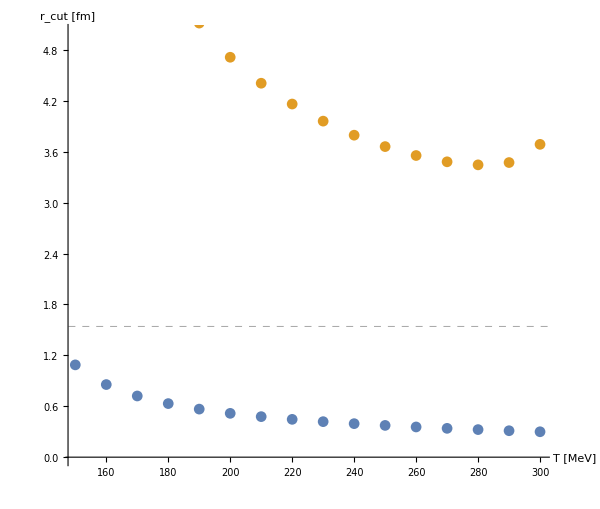

```mathematica
ListPlot[{mdinv,rsbth},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","r_cut [fm]"},ImageSize->{600,600},BaseStyle->{FontSize->14},GridLines->{{},{rsbvac conv}},GridLinesStyle->Directive[Gray, Dashed],PlotRange->{0.,5}]
```

```mathematica
mdTset=Table[{t,mDcalmu[t/1000,0,kfinal[[1]],kfinal[[2]]]},{t,150,300,10}]
```

{{150,0.18137},{160,0.230551},{170,0.273582},{180,0.312444},{190,0.348334},{200,0.382023},{210,0.413042},{220,0.442625},{230,0.471412},{240,0.499536},{250,0.527096},{260,0.554175},{270,0.580837},{280,0.607134},{290,0.63311},{300,0.6588}}

```mathematica
rsbinvth=Table[{t,conv /r/.FindRoot[ReV[r/0.197,mDcalmu[t/1000,0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==0.999ReVas[t/1000],{r,1/10,1/100,10}]},{t,170,300,10}]
```

{{170,0.0308581},{180,0.0349261},{190,0.0385663},{200,0.0418606},{210,0.044768},{220,0.0474055},{230,0.0498178},{240,0.0519926},{250,0.0539019},{260,0.0554948},{270,0.0566782},{280,0.0572684},{290,0.0568204},{300,0.0535138}}

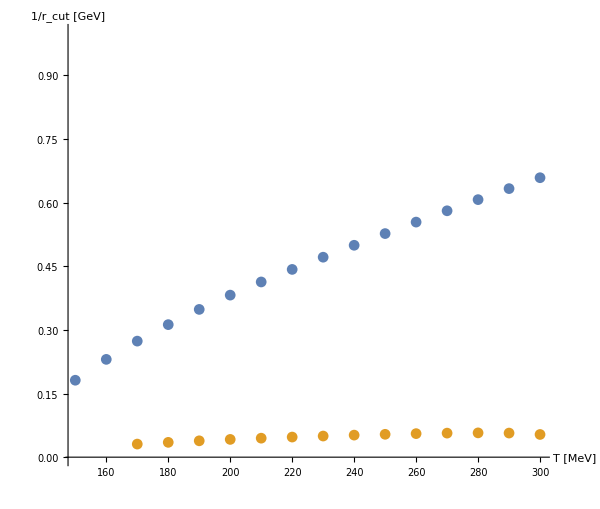

```mathematica
ListPlot[{mdTset,rsbinvth},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","1/r_cut [GeV]"},ImageSize->{600,600},BaseStyle->{FontSize->14},PlotRange->{0.,1}]
```

```mathematica
reg=Table[{1000 Tset[[n]],2π Tset[[n]] rsbinvth[[n,2]]^2/mDcalmu[Tset[[n]],0,kfinal[[1]],kfinal[[2]]]^2},{n,1,Length[Tset]}]
```

{{150.,0.0272821},{160.,0.0230709},{165.,0.0241498},{170.,0.0250073},{180.,0.0232191},{190.,0.0221105},{200.,0.0213697},{250.,0.0152835},{300.,0.0126184}}

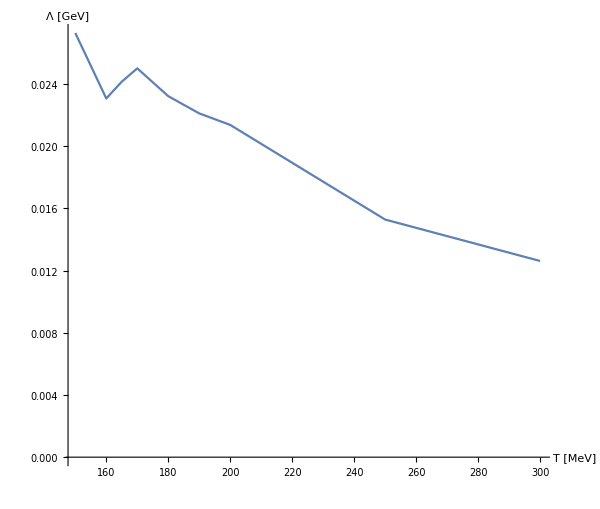

```mathematica
ListPlot[reg,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","Λ [GeV]"},ImageSize->{600,600},BaseStyle->{FontSize->14},PlotRange->All,Joined->True]
```

## Plots for lattice fits

```mathematica
Tlat={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
αlat={0.4859592638209618,0.47104500698378393,0.4561307501466063,0.4374879291001341,0.41884510805366193,0.411387979635073,0.384542317328153};
σlat={0.2088434405704896,0.21706585496978287,0.22528826936907603,0.23556628736819257,0.245844305367309,0.24995551256695564,0.26475585848568345};
clat={1.6313652574133624,1.7808011444057126,1.9302370313980628,2.117031890138499,2.303826748878935,2.37854469237511,2.6475292889613407};
```

```mathematica
mdlat={0.06997549222118046,0.18764366844838265,0.25469933582761983,0.3734921779850663,0.5267111789784007,0.5405169214400376,0.6676534051261366};
```

```mathematica
TlatS={"T=148MeV","T=164MeV","T=182MeV","T=205MeV","T=232MeV","T=243MeV","T=286MeV"};
```

```mathematica
ReVlatplot=Table[ReV[r/conv,mdlat[[l]],αlat[[l]],σlat[[l]],clat[[l]]]-clat[[l]],{l,1,7}];
```

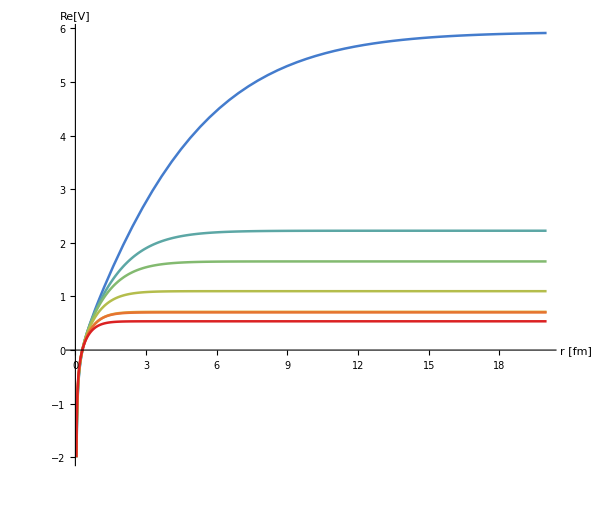

```mathematica
ReVlatanPlot=Plot[ReVlatplot,{r,0.001,20},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[2/8,1,1/8]},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.5,0.5}],BaseStyle->{FontSize->14},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}]
```

```mathematica
ReVlatas[n_]:=clat[[n]]-αlat[[n]]mdlat[[n]]+(2 σlat[[n]])/mdlat[[n]];
```

```mathematica
rsbthlat=Table[{Tlat[[n]],r/.FindRoot[ReV[r/conv,mdlat[[n]],αlat[[n]],σlat[[n]],clat[[n]]]==0.99ReVlatas[n],{r,1/10,1/100,30}]},{n,1,7}]
```

{{0.1478,16.1267},{0.1642,5.63785},{0.1818,4.01413},{0.2054,2.59841},{0.2317,1.74156},{0.2425,1.68421},{0.2861,1.30083}}

```mathematica
rsb9thlat=Table[{Tlat[[n]],r/.FindRoot[ReV[r/conv,mdlat[[n]],αlat[[n]],σlat[[n]],clat[[n]]]==0.999ReVlatas[n],{r,1/10,1/100,30}]},{n,1,7}]
```

{{0.1478,23.436},{0.1642,8.3768},{0.1818,6.0369},{0.2054,3.98248},{0.2317,2.7259},{0.2425,2.64391},{0.2861,2.07953}}

```mathematica
mdlatinv=Table[{Tlat[[n]],conv/mdlat[[n]]},{n,1,7}]
```

{{0.1478,2.81994},{0.1642,1.0516},{0.1818,0.774745},{0.2054,0.52833},{0.2317,0.37464},{0.2425,0.365071},{0.2861,0.295553}}

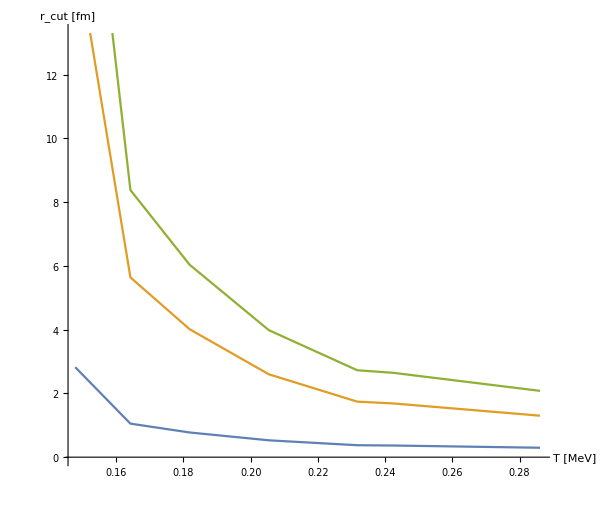

```mathematica
ListPlot[{mdlatinv,rsbthlat,rsb9thlat},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","r_cut [fm]"},ImageSize->{600,600},BaseStyle->{FontSize->14},Joined->True]
```

```mathematica
mdlatset=Table[{Tlat[[n]],mdlat[[n]]},{n,1,7}]
```

{{0.1478,0.0699755},{0.1642,0.187644},{0.1818,0.254699},{0.2054,0.373492},{0.2317,0.526711},{0.2425,0.540517},{0.2861,0.667653}}

```mathematica
rsbinvth=Table[{Tlat[[n]],conv/ r/.FindRoot[ReV[r/0.197,mdlat[[n]],αlat[[n]],σlat[[n]],clat[[n]]]==0.99ReVlatas[n],{r,1/10,1/100,20}]},{n,1,7}]
```

{{0.1478,0.0122563},{0.1642,0.0350585},{0.1818,0.0492397},{0.2054,0.0760676},{0.2317,0.113493},{0.2425,0.117357},{0.2861,0.151945}}

```mathematica
rsbinv9th=Table[{Tlat[[n]],conv/ r/.FindRoot[ReV[r/0.197,mdlat[[n]],αlat[[n]],σlat[[n]],clat[[n]]]==0.999ReVlatas[n],{r,1/10,1/100,30}]},{n,1,7}]
```

{{0.1478,0.0084338},{0.1642,0.0235955},{0.1818,0.032741},{0.2054,0.049631},{0.2317,0.0725099},{0.2425,0.0747585},{0.2861,0.0950479}}

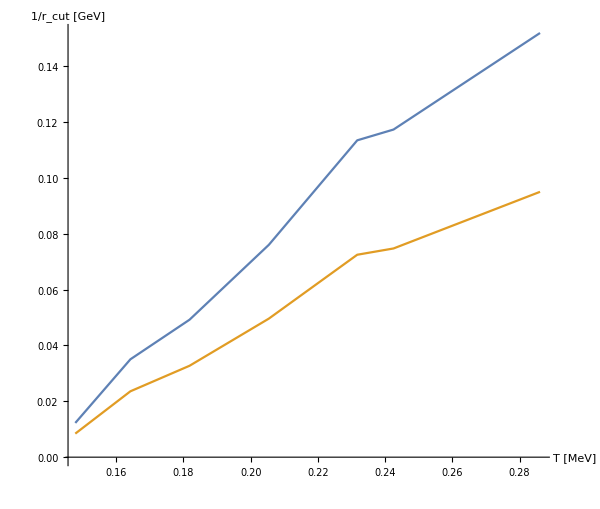

```mathematica
ListPlot[{rsbinvth,rsbinv9th},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","1/r_cut [GeV]"},ImageSize->{600,600},BaseStyle->{FontSize->14},Joined->True]
```

```mathematica
ImVclatplot=Table[ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]],{l,1,7}];
```

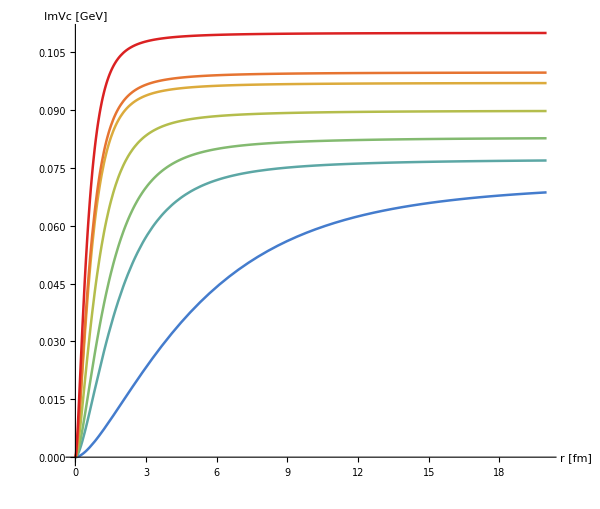

```mathematica
ImVclatanPlot=Plot[ImVclatplot,{r,0.001,20},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[2/8,1,1/8]},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.5,0.5}],BaseStyle->{FontSize->14},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVc [GeV]"},ImageSize->{600,600}]
```

```mathematica
ImVslatplot=ParallelTable[ImVs[r/conv,mdlat[[l]],σlat[[l]],Tlat[[l]]],{l,1,7}];
```

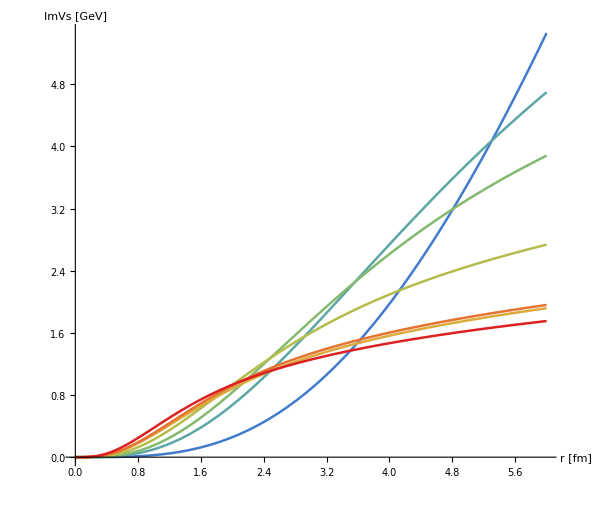

```mathematica
ImVslatanPlot=Plot[ImVslatplot,{r,0.001,6},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[2/8,1,1/8]},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15],{0.5,0.5}],BaseStyle->{FontSize->14},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{600,600}]
```

```mathematica
ImVssblatplot=ParallelTable[ImVssb[r/conv,mdlat[[l]],σlat[[l]],Tlat[[l]],rsb9thlat[[l,2]]/conv],{l,1,7}];
```

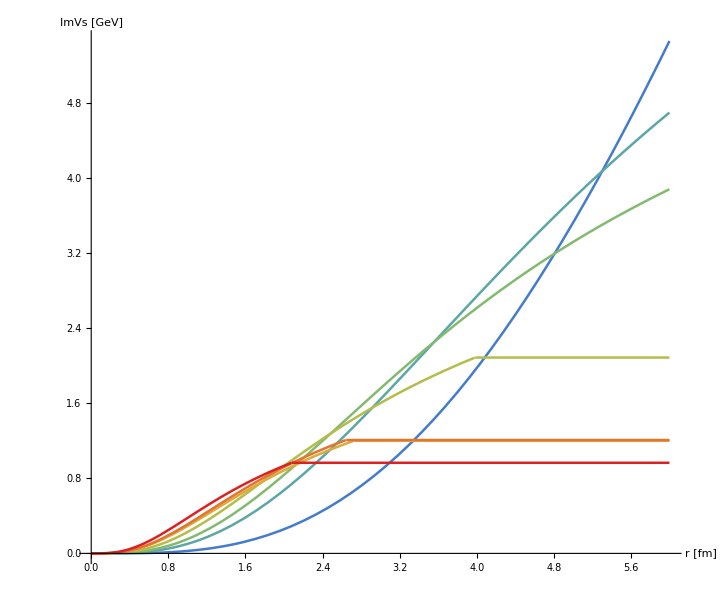

```mathematica
ImVssblatanPlot=Plot[ImVssblatplot,{r,0.001,6},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[2/8,1,1/8]},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.5,0.5}],BaseStyle->{FontSize->14},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{600,600}]
```

### Check ImV for lattice fits with different regulators

```mathematica
ϵp[p_,mD_,T_]:=p^2/(p^2+mD^2)-ⅈ π T(p^2 mD^2)/(p(p^2+mD^2)^2);
```

```mathematica
ϵpreg[p_,mD_,T_,rg_]:=p^2/(p^2+mD^2)-ⅈ π T(p^2 mD^2)/(√(p^2+rg^2)(p^2+mD^2)^2);
```

```mathematica
ϵpreg1[p_,mD_,T_,rg_]:=p^2/(p^2+mD^2)-ⅈ π T(√(p^2+rg^2) mD^2)/((p^2+mD^2)^2);
```

```mathematica
Series[(p^2 mD^2)/(p(p^2+mD^2)^2),{p,0,3}]
```

p/mD^2-(2 p^3)/mD^4+O[p]^4

```mathematica
Series[(p^2 mD^2)/(√(p^2+rg^2)(p^2+mD^2)^2),{p,0,3}]
```

p^2/(mD^2 √(rg^2))+O[p]^4

```mathematica
Series[(√(p^2+rg^2) mD^2)/((p^2+mD^2)^2),{p,0,3}]
```

(√(rg^2))/mD^2+((mD^2-4 rg^2) p^2)/(2 mD^4 √(rg^2))+O[p]^4

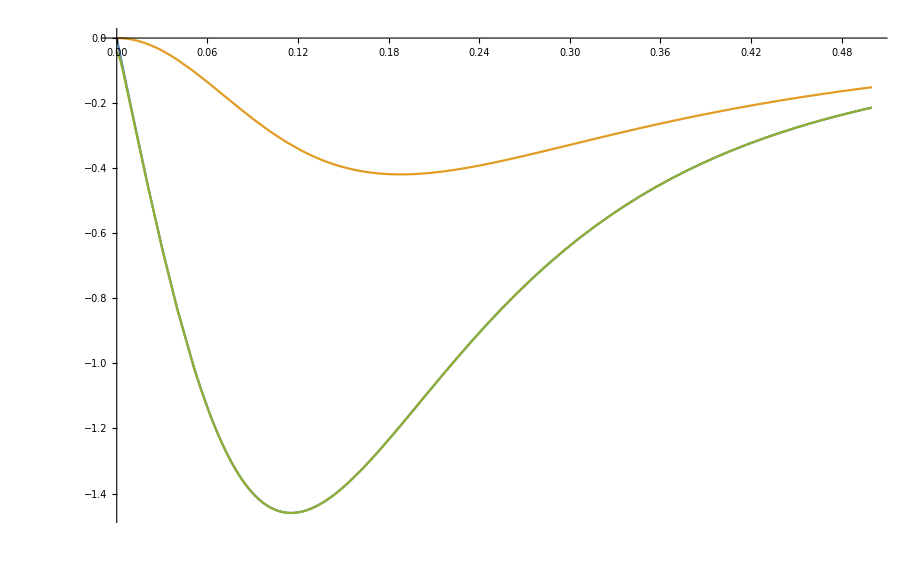

```mathematica
Plot[{Im[ϵp[p,0.2,Tlat[[7]]]],Im[ϵpreg[p,0.2,Tlat[[7]],0.5]],Im[ϵpreg1[p,0.2,Tlat[[7]],0.002]]},{p,0,0.5},PlotRange->All]
```

```mathematica
-4π σ Integrate[Integrate[π T p^2(p mD^2)/((p^2+mD^2)^2)Sinc[p r] r^2(4π)/(2π)^3,r],r]//FullSimplify
```

(2 mD^2 T σ ((2 Cos[p r])/p+r Sin[p r]))/((mD^2+p^2)^2)

```mathematica
Block[{mD=0.2,T=0.155,r=1000,σ=0.17},NIntegrate[(2 mD^2 T σ ((2 Cos[p r])/p+r Sin[p r]))/((mD^2+p^2)^2)-(4 mD^2 T σ)/(p(mD^2+p^2)^2),{p,0,∞}]]
```

-12.8468

```mathematica
rImϵr[r_,mD_,T_,σ_,reg_]:=2 r^2 σ T Quiet[NIntegrate[p^2(p^2 mD^2)/(√(p^2+reg^2)(p^2+mD^2)^2)Sinc[p r],{p,0,∞},MaxRecursion->20]];
```

```mathematica
ImVsder[rth_,mD1_,T1_,σ1_,reg1_]:=Block[{mD=mD1,σ=σ1,T=T1,reg=reg1,tab0,tab1,inter0,inter1,drimvs,imvs,tab2,rϵinter},
rϵinter=Interpolation[Table[Quiet[{r,rImϵr[r,mD,T,σ,reg]}],{r,0,1.5rth,1/100}]];
inter0[r_]:=Quiet[NIntegrate[rϵinter[r1],{r1,0,r},MaxRecursion->20]];
tab1=Table[{r,inter0[r]},{r,0,1.5rth,1/100}];
drimvs=Interpolation[tab1];
inter1[r_]:=NIntegrate[drimvs[r1],{r1,0,r}];
tab2=Table[{r,inter1[r]},{r,0,1.5rth,1/100}];
imvs=Interpolation[tab2];
Return[drimvs[rth]/imvs[rth]]];
```

```mathematica
ImVsinter[rth_,mD1_,T1_,σ1_,reg1_]:=Block[{mD=mD1,σ=σ1,T=T1,reg=reg1,tab0,tab1,inter0,inter1,drimvs,imvs,tab2,rϵinter},
rϵinter=Interpolation[Table[Quiet[{r,rImϵr[r,mD,T,σ,reg]}],{r,0,1.5rth,1/100}]];
inter0[r_]:=Quiet[NIntegrate[rϵinter[r1],{r1,0,r},MaxRecursion->20]];
tab1=Table[{r,inter0[r]},{r,0,1.5rth,1/100}];
drimvs=Interpolation[tab1];
inter1[r_]:=NIntegrate[drimvs[r1],{r1,0,r}];
tab2=Table[{r,inter1[r]},{r,0,1.5rth,1/100}];
imvs=Interpolation[tab2];
Return[imvs]];
```

```mathematica
ImVsregTab[mD1_,σ1_,T1_,reg1_,n_]:=Block[{mD=mD1,σ=σ1,T=T1,reg=reg1,tab0,tab1,inter0,inter1,inter2,tab2,rϵinter},
rϵinter=Interpolation[ParallelTable[Quiet[{r,rImϵr[r,mD,T,σ,reg]}],{r,0,150,1/100}]];
inter0[r_]:=Quiet[NIntegrate[rϵinter[r1],{r1,0,r},MaxRecursion->20]];
tab1=ParallelTable[{r,inter0[r]},{r,0,150,1/100}];
inter1=Interpolation[tab1];
inter2[r_]:=NIntegrate[inter1[r1],{r1,0,r}];
tab2=ParallelTable[{r,inter2[r]},{r,0,150,1/100}];
Export["mathematica/reg_pot/ImVsT1reg"<>ToString[n]<>".dat",tab2];
Return[Interpolation[tab2]]];
```

```mathematica
ImVsT1interreg05=ImVsregTab[mdlat[[1]],σlat[[1]],Tlat[[1]],0.05,05];
ImVsT1interreg10=ImVsregTab[mdlat[[1]],σlat[[1]],Tlat[[1]],0.1,10];
ImVsT1interreg15=ImVsregTab[mdlat[[1]],σlat[[1]],Tlat[[1]],0.15,15];
ImVsT1interreg20=ImVsregTab[mdlat[[1]],σlat[[1]],Tlat[[1]],0.2,20];
```

```mathematica
ImVsT1interreg015=ImVsregTab[mdlat[[1]],σlat[[1]],Tlat[[1]],0.015,015];
```

```mathematica
ImVsT1interreg30=ImVsregTab[mdlat[[1]],σlat[[1]],Tlat[[1]],0.3,30];
```

```mathematica
rsb9thlat
```

{{0.1478,23.436},{0.1642,8.3768},{0.1818,6.0369},{0.2054,3.98248},{0.2317,2.7259},{0.2425,2.64391},{0.2861,2.07953}}

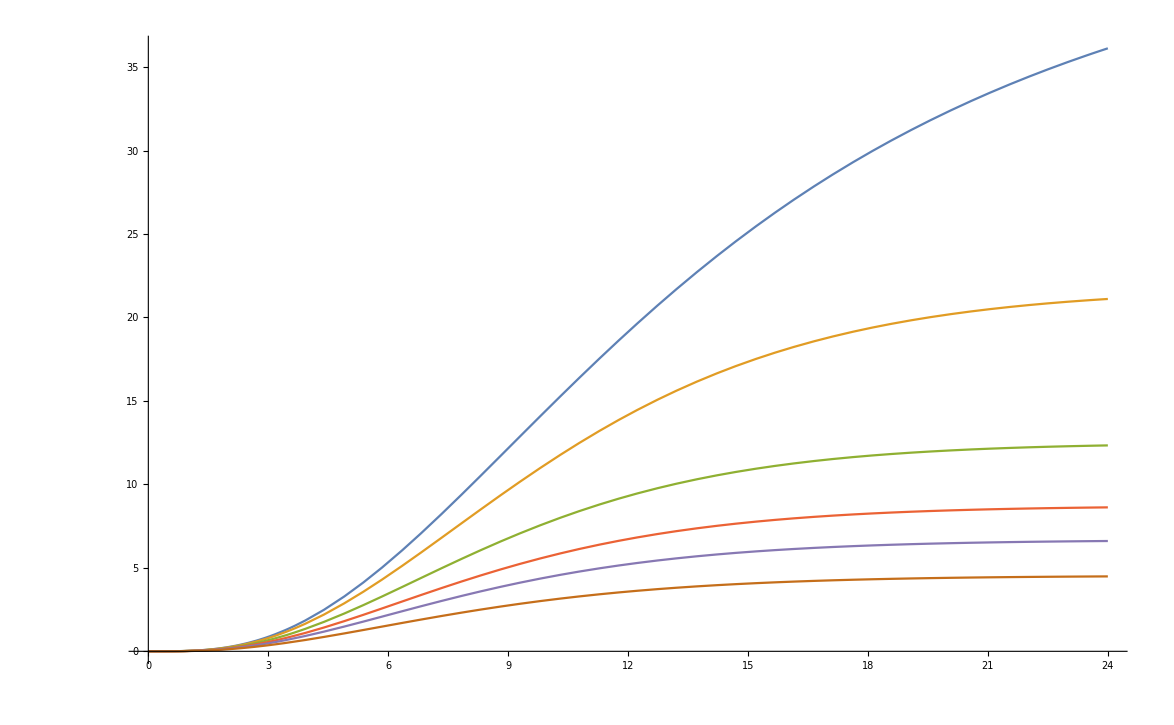

```mathematica
Plot[{ImVsT1interreg015[x/conv],ImVsT1interreg05[x/conv],ImVsT1interreg10[x/conv],ImVsT1interreg15[x/conv],ImVsT1interreg20[x/conv],ImVsT1interreg30[x/conv]},{x,0,24}]
```

```mathematica
2 σ T mD^2 Integrate[Integrate[r1^2 p^4/((p^2+Δ^2)^(1/2)(p^2+mD^2)^2)Sinc[p r1],{r1,0,r2}],{r2,0,r}]//Simplify
```

-(2 mD^2 T σ (-2+2 Cos[p r]+p r Sin[p r]))/((mD^2+p^2)^2 √(p^2+Δ^2))

```mathematica
check=Block[{mD=mdlat[[1]],Δ=0.3,σ=σlat[[1]],T=Tlat[[1]]},Interpolation[ParallelTable[{r,NIntegrate[-(2 mD^2 T σ (-2+2 Cos[p r/conv]+p r/conv Sin[p r/conv]))/((mD^2+p^2)^2 √(p^2+Δ^2)),{p,0,∞}]},{r,0.01,24,0.01}]]];
```

```mathematica
Block[{mD=mdlat[[1]],Δ=0.3,σ=σlat[[1]],T=Tlat[[1]]},2 mD^2 T σ NIntegrate[2/((mD^2+p^2)^2 √(p^2+Δ^2)),{p,0,∞}]]
```

4.53145

```mathematica
Block[{mD=mdlat[[1]],Δ=0.3,σ=σlat[[1]],T=Tlat[[1]],r=10000000},NIntegrate[(2 mD^2 T σ (2-2 Cos[p r]-p r Sin[p r]))/((mD^2+p^2)^2 √(p^2+Δ^2)),{p,0,∞}]]
```

4.53145

InterpolatingFunction::dmval: Input value {0.000490286} lies outside the range of data in the interpolating function. Extrapolation will be used.

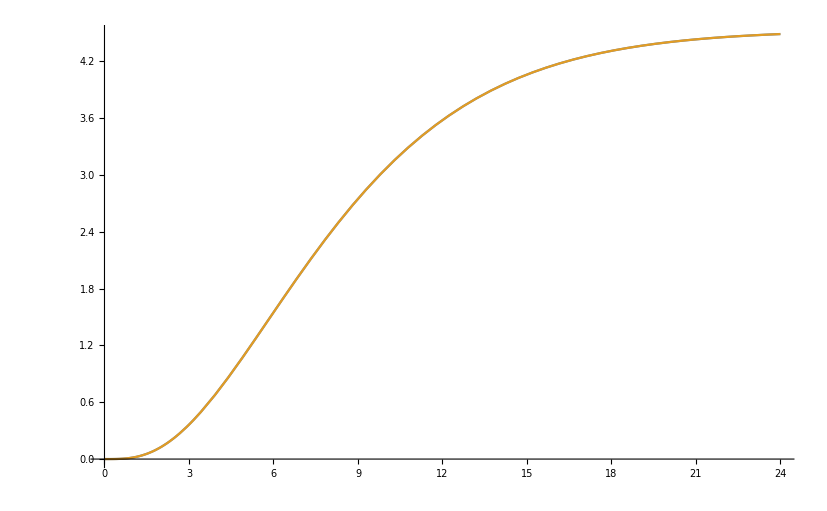

```mathematica
Plot[{ImVsT1interreg30[x/conv],check[x]},{x,0,24}]
```

```mathematica
ImVsT1intersb9=ImVsregTab[mdlat[[1]],σlat[[1]],Tlat[[1]],rsbinv9th[[1,2]],1];
ImVsT2intersb9=ImVsregTab[mdlat[[2]],σlat[[2]],Tlat[[2]],rsbinv9th[[2,2]],2];
ImVsT3intersb9=ImVsregTab[mdlat[[3]],σlat[[3]],Tlat[[3]],rsbinv9th[[3,2]],3];
ImVsT4intersb9=ImVsregTab[mdlat[[4]],σlat[[4]],Tlat[[4]],rsbinv9th[[4,2]],4];
ImVsT5intersb9=ImVsregTab[mdlat[[5]],σlat[[5]],Tlat[[5]],rsbinv9th[[5,2]],5];
ImVsT6intersb9=ImVsregTab[mdlat[[6]],σlat[[6]],Tlat[[6]],rsbinv9th[[6,2]],6];
ImVsT7intersb9=ImVsregTab[mdlat[[7]],σlat[[7]],Tlat[[7]],rsbinv9th[[7,2]],7];
```

```mathematica
ImVsT1intersb=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsrregT1.dat"]]];
ImVsT2intersb=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsrregT2.dat"]]];
ImVsT3intersb=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsrregT3.dat"]]];
ImVsT4intersb=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsrregT4.dat"]]];
ImVsT5intersb=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsrregT5.dat"]]];
ImVsT6intersb=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsrregT6.dat"]]];
ImVsT7intersb=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsrregT7.dat"]]];
```

```mathematica
ImVsT1intersb9=Interpolation[ToExpression[Import["mathematica/reg_pot/ImVsregsb9T1.dat"]]];
ImVsT2intersb9=Interpolation[ToExpression[Import["mathematica/reg_pot/ImVsregsb9T2.dat"]]];
ImVsT3intersb9=Interpolation[ToExpression[Import["mathematica/reg_pot/ImVsregsb9T3.dat"]]];
ImVsT4intersb9=Interpolation[ToExpression[Import["mathematica/reg_pot/ImVsregsb9T4.dat"]]];
ImVsT5intersb9=Interpolation[ToExpression[Import["mathematica/reg_pot/ImVsregsb9T5.dat"]]];
ImVsT6intersb9=Interpolation[ToExpression[Import["mathematica/reg_pot/ImVsregsb9T6.dat"]]];
ImVsT7intersb9=Interpolation[ToExpression[Import["mathematica/reg_pot/ImVsregsb9T7.dat"]]];
```

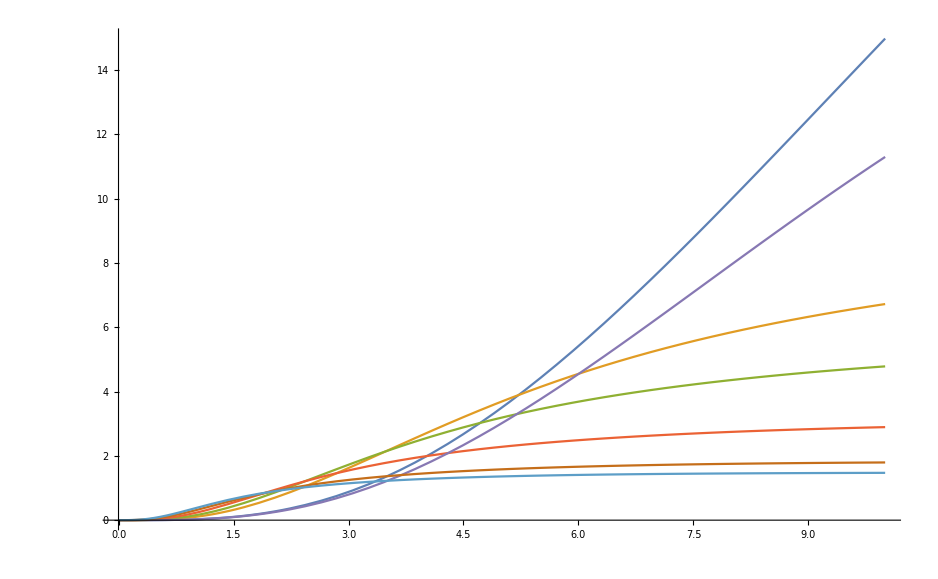

```mathematica
Plot[{ImVsT1intersb9[r/conv],ImVsT2intersb9[r/conv],ImVsT3intersb9[r/conv],ImVsT4intersb9[r/conv],ImVsT5intersb9[r/conv],ImVsT6intersb9[r/conv],ImVsT7intersb9[r/conv]},{r,0,10}]
```

### Include lattice data

```mathematica
Needs["ErrorBarPlots`"];
Vdata=SplitBy[Import["latticedata/AllData2p1Flavors/Vall.txt","Table"],First];

ImVdataT[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataTe[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]],Vdata[[n,x,6]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataTn[n_]:=ImVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ImVdataTne[n_]:=ImVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};
```

```mathematica
Shift=1.
```

1.

```mathematica
For[l=1,l≤ 7,l++,PotImRescale[l]=ImVdataTe[l]/.{a_,b_,c_}:>{a-Shift*l+7*Shift,b,c}];
```

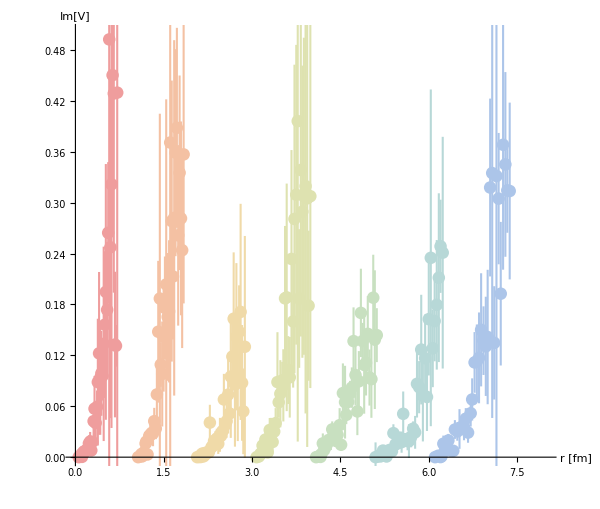

```mathematica
ImVdatPlot=ErrorListPlot[Table[PotImRescale[l][[1;;Floor[Length[PotImRescale[l]]*0.9]]],{l,1,7}],PlotRange->{{0,8},{0,0.5}},PlotStyle->Thread@{AbsolutePointSize[9],AbsoluteThickness[1.5],Lighter[Lighter[ColorData["Rainbow"]/@Range[2/8,1,1/8]]]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->16},AspectRatio->0.85,PlotRange->{0,0.35},AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

```mathematica
ImVtab[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT1inter[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,2,1/100}]];
ImVtab[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT2inter[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,3,1/100}]];
ImVtab[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT3inter[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,4,1/100}]];
ImVtab[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT4inter[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,5,1/100}]];
ImVtab[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT5inter[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,6,1/100}]];
ImVtab[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT6inter[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,7,1/100}]];
ImVtab[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT7inter[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,8,1/100}]];
```

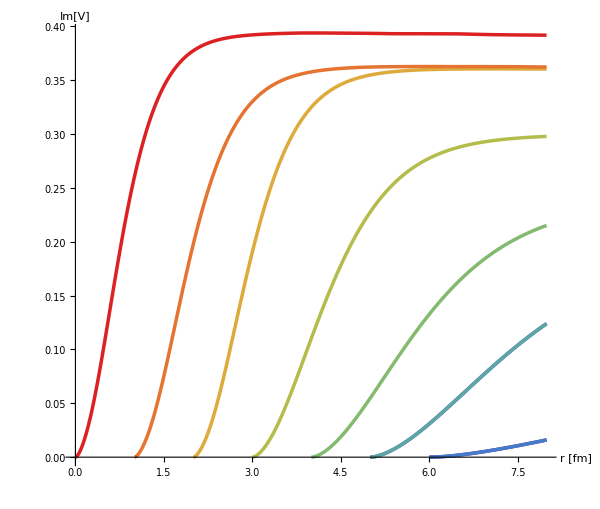

```mathematica
ImVPlot=ListPlot[{ImVtab[1,0],ImVtab[2,0],ImVtab[1,0],ImVtab[2,0],ImVtab[3,0],ImVtab[4,0],ImVtab[5,0],ImVtab[6,0],ImVtab[7,0]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

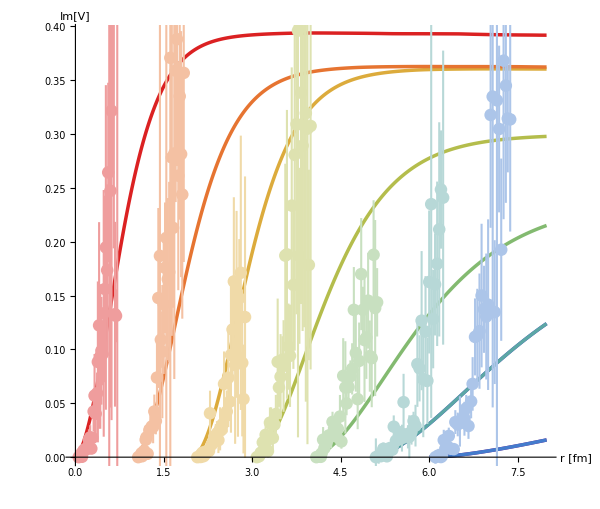

```mathematica
Show[ImVPlot,ImVdatPlot]
```

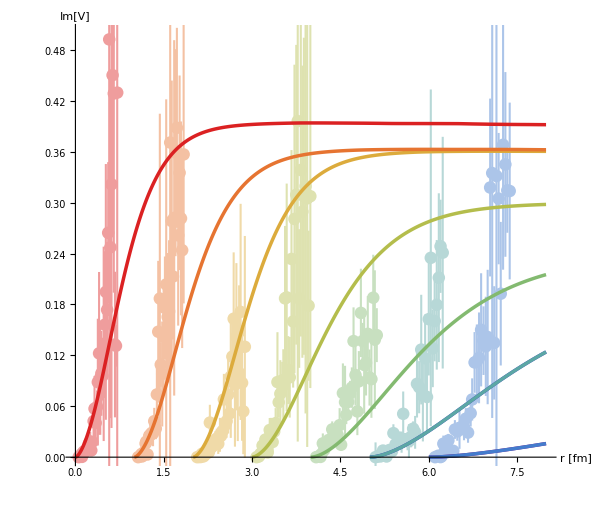

```mathematica
Show[ImVdatPlot,ImVPlot]
```

```mathematica
ImVesb[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT1intersb[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,2,1/100}]];
ImVesb[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT2intersb[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,3,1/100}]];
ImVesb[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT3intersb[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,4,1/100}]];
ImVesb[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT4intersb[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,5,1/100}]];
ImVesb[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT5intersb[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,6,1/100}]];
ImVesb[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT6intersb[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,7,1/100}]];
ImVesb[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT7intersb[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,8,1/100}]];
```

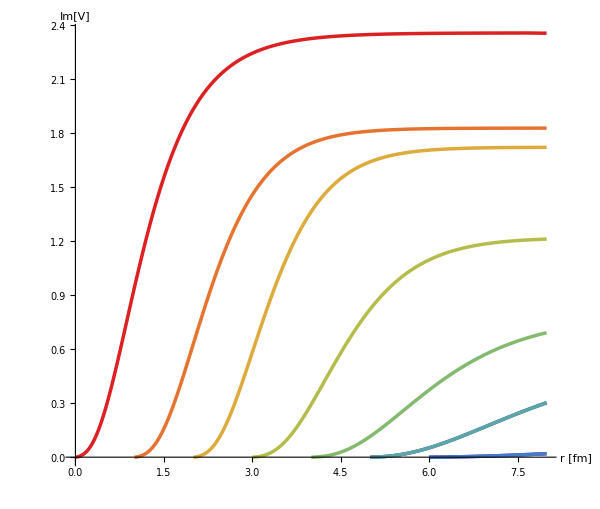

```mathematica
ImVPlotsb=ListPlot[{ImVesb[1,0],ImVesb[2,0],ImVesb[1,0],ImVesb[2,0],ImVesb[3,0],ImVesb[4,0],ImVesb[5,0],ImVesb[6,0],ImVesb[7,0]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

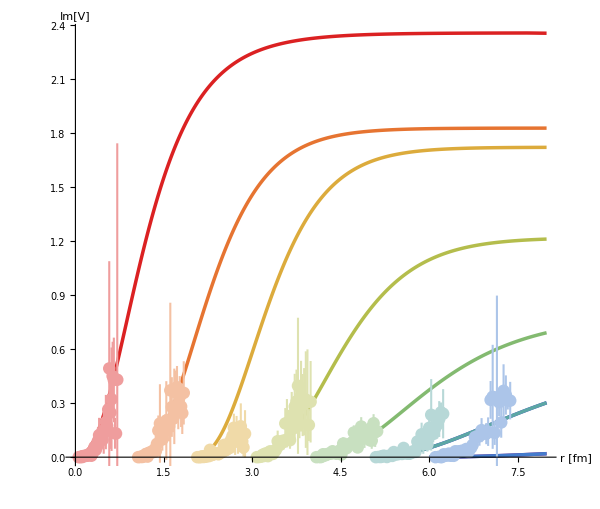

```mathematica
Show[ImVPlotsb,ImVdatPlot]
```

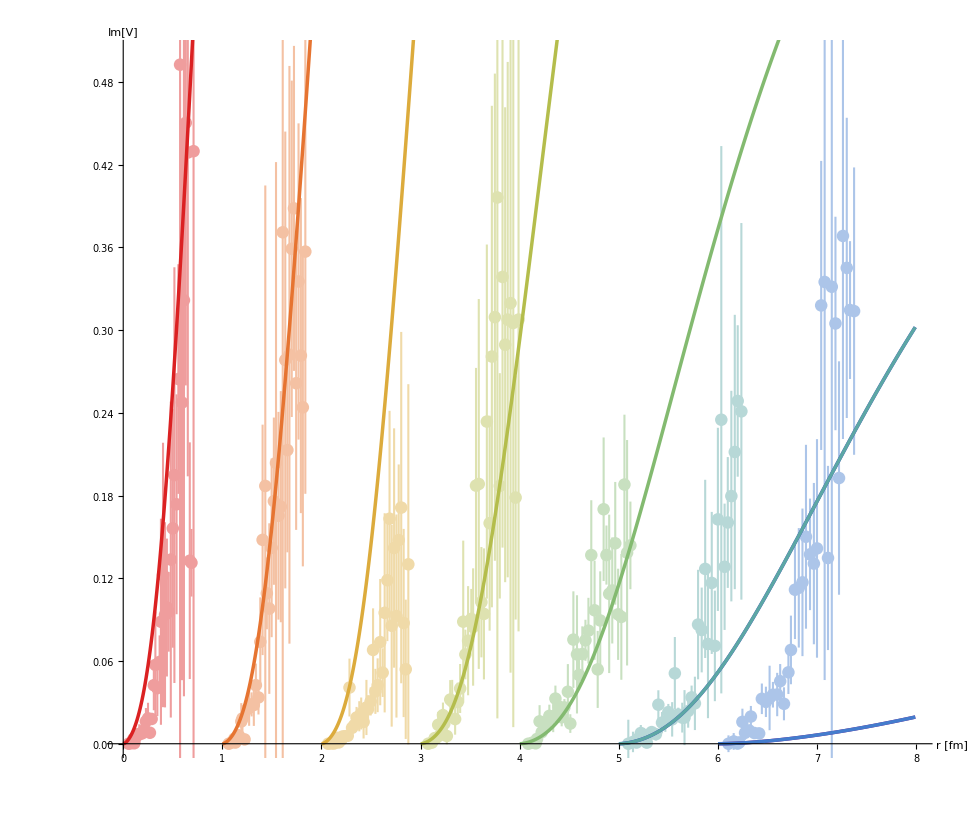

```mathematica
Show[ImVdatPlot,ImVPlotsb]
```

```mathematica
ImVemd[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT1interMD[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,2,1/100}]];
ImVemd[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT2interMD[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,3,1/100}]];
ImVemd[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT3interMD[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,4,1/100}]];
ImVemd[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT4interMD[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,5,1/100}]];
ImVemd[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT5interMD[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,6,1/100}]];
ImVemd[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT6interMD[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,7,1/100}]];
ImVemd[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT7interMD[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,8,1/100}]];
```

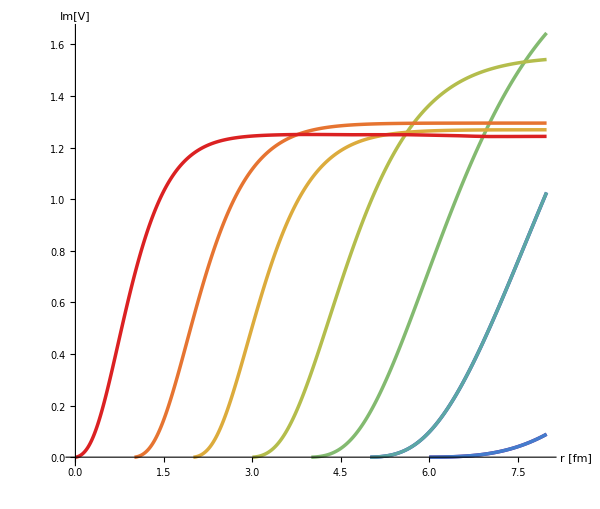

```mathematica
ImVPlotmd=ListPlot[{ImVemd[1,0],ImVemd[2,0],ImVemd[1,0],ImVemd[2,0],ImVemd[3,0],ImVemd[4,0],ImVemd[5,0],ImVemd[6,0],ImVemd[7,0]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

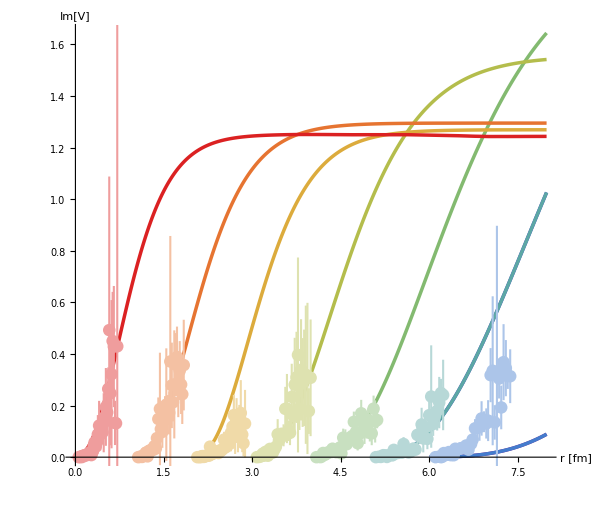

```mathematica
Show[ImVPlotmd,ImVdatPlot]
```

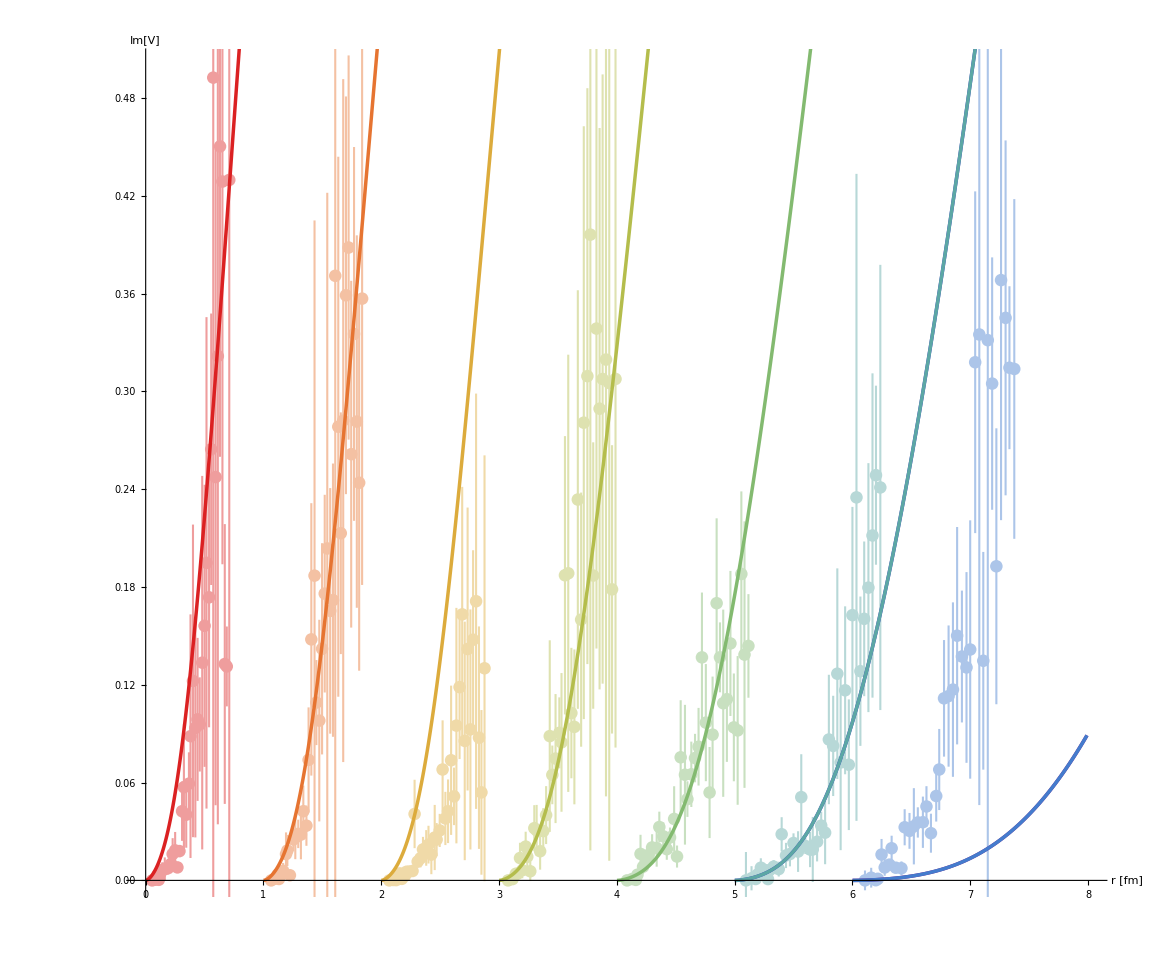

```mathematica
Show[ImVdatPlot,ImVPlotmd]
```

```mathematica
ImVesb9[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT1intersb9[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,2,1/100}]];
ImVesb9[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT2intersb9[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,3,1/100}]];
ImVesb9[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT3intersb9[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,4,1/100}]];
ImVesb9[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT4intersb9[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,5,1/100}]];
ImVesb9[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT5intersb9[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,6,1/100}]];
ImVesb9[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT6intersb9[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,7,1/100}]];
ImVesb9[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsT7intersb9[r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,8,1/100}]];
```

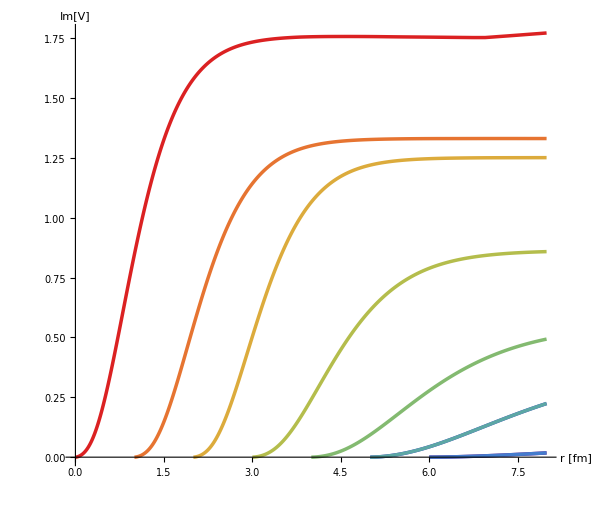

```mathematica
ImVPlotsb9=ListPlot[{ImVesb9[1,0],ImVesb9[2,0],ImVesb9[1,0],ImVesb9[2,0],ImVesb9[3,0],ImVesb9[4,0],ImVesb9[5,0],ImVesb9[6,0],ImVesb9[7,0]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

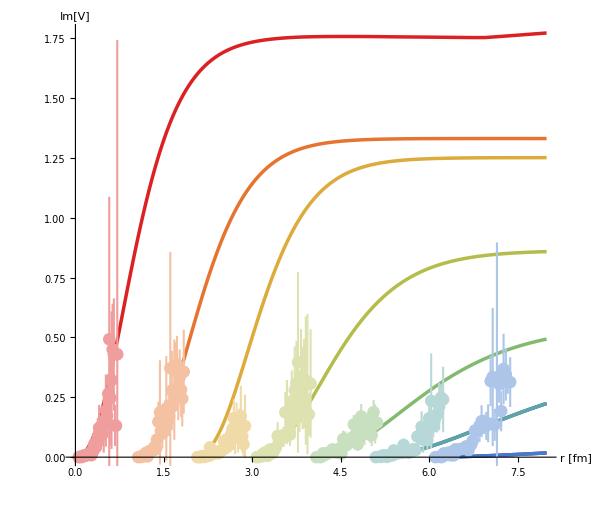

```mathematica
Show[ImVPlotsb9,ImVdatPlot]
```

```mathematica
Show[ImVdatPlot,ImVPlotsb9]
```

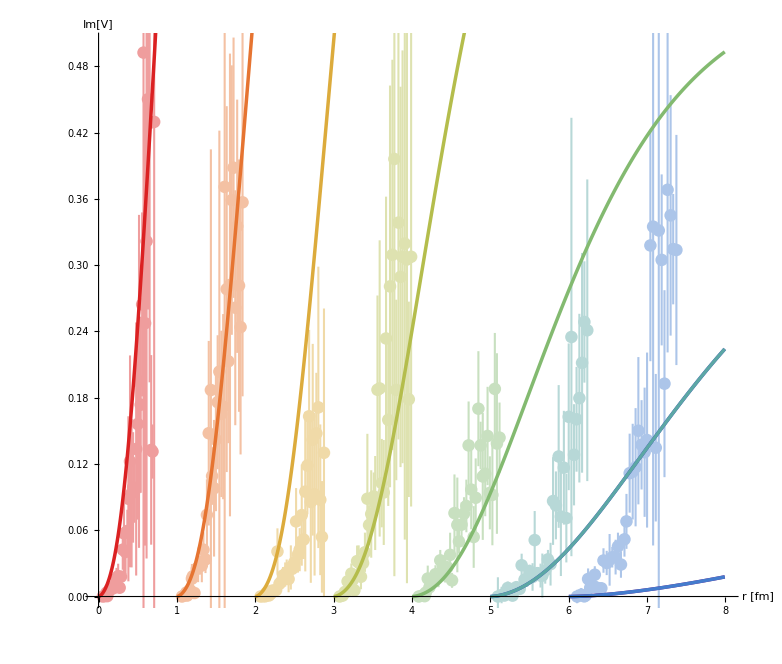

```mathematica
ImVsb[r_,mD_,α_,σ_,T_,rsb_]:=If[r<rsb,T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 (r/conv)^2)/4])+1/4 mD √π (r/conv)^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 (r/conv)^2)/4],T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 (rsb/conv)^2)/4])+1/4 mD √π (rsb/conv)^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 (rsb/conv)^2)/4]];
```

```mathematica
ImVesbcheck[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r,mdlat[[1]],αlat[[1]],σlat[[1]],Tlat[[1]], rsb9thlat[[1,2]]]},{r,1/1000,2,1/100}]];
ImVesbcheck[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r,mdlat[[2]],αlat[[2]],σlat[[2]],Tlat[[2]],rsb9thlat[[2,2]]]},{r,1/1000,3,1/100}]];
ImVesbcheck[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r,mdlat[[3]],αlat[[3]],σlat[[3]],Tlat[[3]],rsb9thlat[[3,2]]]},{r,1/1000,4,1/100}]];
ImVesbcheck[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r,mdlat[[4]],αlat[[4]],σlat[[4]],Tlat[[4]],rsb9thlat[[4,2]]]},{r,1/1000,5,1/100}]];
ImVesbcheck[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r,mdlat[[5]],αlat[[5]],σlat[[5]],Tlat[[5]],rsb9thlat[[5,2]]]},{r,1/1000,6,1/100}]];
ImVesbcheck[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r,mdlat[[6]],αlat[[6]],σlat[[6]],Tlat[[6]],rsb9thlat[[6,2]]]},{r,1/1000,7,1/100}]];
ImVesbcheck[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r,mdlat[[7]],αlat[[7]],σlat[[7]],Tlat[[7]],rsb9thlat[[7,2]]]},{r,1/1000,8,1/100}]];
```

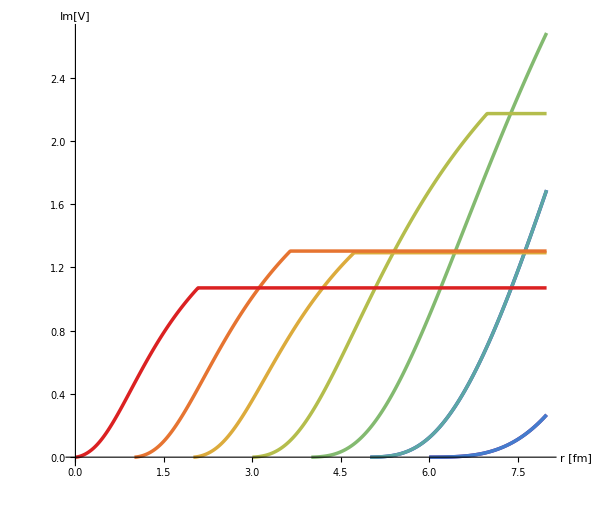

```mathematica
ImVPlotsbcheck=ListPlot[{ImVesbcheck[1,0],ImVesbcheck[2,0],ImVesbcheck[1,0],ImVesbcheck[2,0],ImVesbcheck[3,0],ImVesbcheck[4,0],ImVesbcheck[5,0],ImVesbcheck[6,0],ImVesbcheck[7,0]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```